Question for: http://mathematica.stackexchange.com/questions/40066/how-to-avoid-an-expensive-subset-of-a-manipulate-computation-when-dependent-vari

```mathematica
ClearAll[preCalculateStuff]
preCalculateStuff = (#1  #2 ) & ;

Manipulate[ 
DynamicModule[{f},
f=preCalculateStuff[a,b];
{f, Dynamic@Plot[(f t) Sin[  t + r ],{r, 0, 2 Pi}]}
],
{{a,0.5},0,1},
{{b,0.5},0,1},
{{t,0.5},0,1,ContinuousAction->True},
ContinuousAction->None
]
```

```mathematica
Manipulate[tick;
Grid[{{Row[{"f=",f," a=",a," b=",b," t=",t, " tick=", tick}]},{Plot[(f t) Sin[t+r],{r,0,2 Pi},ImagePadding->30,ImageSize->400,Frame->True]}}],
Grid[{
{"a",Manipulator[Dynamic[a,{a=#;f=preCalculateStuff[a,b];tick=Not[tick]}&],{0,1,0.01}],Dynamic[a]},
{"b",Manipulator[Dynamic[b,{b=#;f=preCalculateStuff[a,b];tick=Not[tick]}&],{0,1,0.01}],Dynamic[b]},
{"t",Manipulator[Dynamic[t,{t=#;tick=Not[tick]}&],{0,1,0.01}],Dynamic[t]}},Alignment->Center,Spacings->{.5,.5}],{{tick,False},None},
{{a,.5},None},
{{b,.4},None},
{{t,.7},None},
{{f,.5*.4},None},
TrackedSymbols:>{tick},
Initialization:>(preCalculateStuff[a_,b_]:=Module[{},(*heavy computation goes here*)a*b])]
```

```mathematica
(*Module[{turns = 10, o = {1,2}},
{Manipulate[ParametricPlot[RotationMatrix[ArcTan@@r].(o + {x,Sin[2 Pi turns x/Norm[r]]}),{x,0,Norm[r]},PlotRange->5],{{r,{1,1}},Locator}],
Manipulate[ParametricPlot[{x,Sin[2 Pi turns x/Norm[r]]} + o,{x,0,Norm[r]},PlotRange->5],{{r,{1,1}},Locator}]}
]*)
```

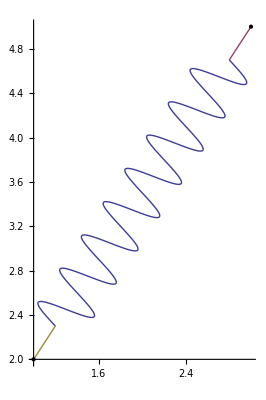

```mathematica
ClearAll[spring]
spring::usage = "spring[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds ]" ;
spring[ a1_List, a2_List, n_:8,h_:.25, f_: 0.1 ] :=Module[{n1, d, nd, r, r1 },
n1 = Norm[a1] ;
d = a2 - a1 ;
nd = Norm[d] ;
r = RotationMatrix[ArcTan @@  d ] ;
r1 = r . {n1, 0} ;
ParametricPlot[ 
{
{a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}},
{a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}},
{a1 -r1 + r . { n1 +t f nd, 0}}
}
, {t, 0, 1 }
, Epilog->{ Point[{a1, a2}]}
]
]

spring[ {1,2}, {3,5} ]
```

```mathematica
?spring
```

spring[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds]

```mathematica
(* Based on: http://mathematica.stackexchange.com/a/37228/10 *)
(*
ClearAll[ unitSpringPoints, coordinateTrasformMatrix, coordinateTransform, spring ] ;

unitSpringPoints::usage = "This is a spring connecting {0,0} and {1,0} with two small horizontal segment at the end points (that is the reason for generating two separate lists).To show the spring just wrap a Line around the generated points,like this

Show[Graphics[Line[unitSpringPoints[5,0.25]]]]" ;
unitSpringPoints[n_,h_]:=Block[{dl,xlist,ylist},dl=1/(2 n+1);
xlist=Flatten[{0,1.5 dl,dl Table[k,{k,2,2 n-1}],1-1.5 dl,1}];
ylist=Flatten[{0,0,h/2 Table[(-1)^(k+1),{k,2,2 n-1}],0,0}];
Transpose[{xlist,ylist}]]

coordinateTrasformMatrix::usage = "Next I defined a function to transform coordinates in order to produce a spring between two given points {x0,y0} and {x1,y1}.Since this is very old code,I defined my own transformation matrix as in" ;
coordinateTrasformMatrix[{x0_,y0_},{x1_,y1_}]:=Block[{theta},theta=ArcTan[(x1-x0),(y1-y0)];
{{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}}] ;


coordinateTransform::usage = "And then I used it to transform the coordinates of the points of the the unit spring in those of the points of the spring between the given points" ;
coordinateTransform[coords_List,{{x0_,y0_},{x1_,y1_}}]:=Block[{scale,mat},scale=Sqrt[(x1-x0)^2+(y1-y0)^2];
mat=coordinateTrasformMatrix[{x0,y0},{x1,y1}];
({x0,y0}+mat.({scale,1}*#))&/@coords] ;

spring::usage = "Then,a spring with n coils and aspect ratio h between points {x0,y0} and {x1,y1} would be given by
For example:

Show[Graphics[spring[{{2,2},{3,3}},8,0.25]],AspectRatio→Automatic]
Show[Graphics[spring[{{0,0},{0,1}},8,0.25]],AspectRatio→Automatic]" ;
spring[{{x0_,y0_},{x1_,y1_}},n_:8,h_:.25]:=Line[coordinateTransform[unitSpringPoints[n,h],{{x0,y0},{x1,y1}}]] ;*)
```